```mathematica
xlist=Table[x0,i,20];
zlist=Table[z0,i,20];
xlist[[i_]]:=Exp[-t/T2]*(xlist[[(i-1)]]*Cos[p*i]*Exp[-t/T2]+zlist[[i-1]]*Sin[p*i]*Exp[-t/T1])
```

```mathematica
zlist[i_]:=Exp[-t/T1]*(xlist[(i-1)]*Sin[p*i]*Exp[-t/T2]+zlist[i-1]*Cos[p*i]*Exp[-t/T1])
```

```mathematica
2*0.4*0.4*90/Pi
```

```mathematica
0.22/24
```

0.00916667

```mathematica
0.0068/0.4
```

0.017

```mathematica
Manipulate[
p=(180-d)*Pi/90;
n=60;
x0=2.0;
z0=f*2.0;
t=0.8;
x[0]=x0;
z[0]=z0;
xlist=Table[x0,{i,n}];
zlist=Table[z0,{i,n}];
For[i=2,i<=n,i++,xlist[[i]]=(E^(-t/T2)*(xlist[[(i-1)]]*Cos[p]*Exp[-t/T2]+zlist[[(i-1)]]*Sin[p]*Exp[-t/T1])//N);zlist[[i]]=((Exp[-t/T1]*(-xlist[[(i-1)]]*Sin[p]*Exp[-t/T2]+zlist[[(i-1)]]*Cos[p]*Exp[-t/T1]))//N)]
(For[i=2,i<n,i++,xlist[[i]]=Abs[xlist[[i]]]])
fkt=Abs[q[tt]]/.DSolve[{q'[tt]==-1/(T1) q[tt]+w*y[tt],y'[tt]==-1/(T2) y[tt]-w*q[tt],q[0]==x0,y[0]==z0},{q[tt],y[tt]},tt];
Show[ListPlot[xlist,PlotRange->{{0,60},{0,3}}],ListPlot[cp005,PlotStyle->Red]],{d,11,14},{T1,7,20},{T2,7,20},{f,0.00,1}]
```

```mathematica
Manipulate[
p=(180-d)*Pi/90;
n=60;
x0=2.0;
z0=f*2.0;
t=0.6;
x[0]=x0;
z[0]=z0;
xlist=Table[x0,{i,n}];
zlist=Table[z0,{i,n}];
For[i=2,i<=n,i++,xlist[[i]]=(E^(-t/T2)*(xlist[[(i-1)]]*Cos[p]*Exp[-t/T2]+zlist[[(i-1)]]*Sin[p]*Exp[-t/T1])//N);zlist[[i]]=((Exp[-t/T1]*(-xlist[[(i-1)]]*Sin[p]*Exp[-t/T2]+zlist[[(i-1)]]*Cos[p]*Exp[-t/T1]))//N)]
(For[i=2,i<=n,i++,xlist[[i]]=Abs[xlist[[i]]]])
fkt=Abs[q[tt]]/.DSolve[{q'[tt]==-1/(T1) q[tt]+w*y[tt],y'[tt]==-1/(T2) y[tt]-w*q[tt],q[0]==x0,y[0]==z0},{q[tt],y[tt]},tt];
Show[ListPlot[xlist,PlotRange->{{0,60},{0,3}}],ListPlot[cp01,PlotStyle->Red]],{d,11,14},{T1,7,20},{T2,7,20},{f,0.00,1}]
```

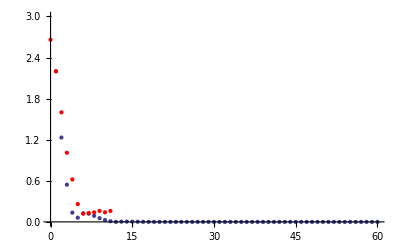

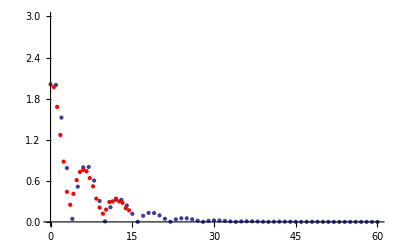

```mathematica
x0=2.2;
z0=f*x0;
t=1/2;
T1=4.25/2;
T2=4.5/2;
x[0]=x0;
z[0]=z0;
xlist=Table[x0,{i,n}];
zlist=Table[z0,{i,n}];
For[i=2,i<=n,i++,xlist[[i]]=(E^(-t/T2)*(xlist[[(i-1)]]*Cos[p]*Exp[-t/T2]+zlist[[(i-1)]]*Sin[p]*Exp[-t/T1])//N);zlist[[i]]=((Exp[-t/T1]*(-xlist[[(i-1)]]*Sin[p]*Exp[-t/T2]+zlist[[(i-1)]]*Cos[p]*Exp[-t/T1]))//N)]
(For[i=2,i<=n,i++,xlist[[i]]=Abs[xlist[[i]]]])
fkt=Abs[q[tt]]/.DSolve[{q'[tt]==-1/(T1) q[tt]+w*y[tt],y'[tt]==-1/(T2) y[tt]-w*q[tt],q[0]==x0,y[0]==z0},{q[tt],y[tt]},tt];
Show[ListPlot[xlist,PlotRange->{{0,60},{0,3}}],ListPlot[cp02,PlotStyle->Red]]

p=180-Pi/90*11.5;
x0=2.0;
z0=f*x0;
t=0.3;
T1=10/2;
T2=6.5/2;
x[0]=x0;
z[0]=z0;
xlist=Table[x0,{i,n}];
zlist=Table[z0,{i,n}];
For[i=2,i<=n,i++,xlist[[i]]=(E^(-t/T2)*(xlist[[(i-1)]]*Cos[p]*Exp[-t/T2]+zlist[[(i-1)]]*Sin[p]*Exp[-t/T1])//N);zlist[[i]]=((Exp[-t/T1]*(-xlist[[(i-1)]]*Sin[p]*Exp[-t/T2]+zlist[[(i-1)]]*Cos[p]*Exp[-t/T1]))//N)]
(For[i=2,i<=n,i++,xlist[[i]]=Abs[xlist[[i]]]])
fkt=Abs[q[tt]]/.DSolve[{q'[tt]==-1/(T1) q[tt]+w*y[tt],y'[tt]==-1/(T2) y[tt]-w*q[tt],q[0]==x0,y[0]==z0},{q[tt],y[tt]},tt];
Show[ListPlot[xlist,PlotRange->{{0,60},{0,3}}],ListPlot[cp01,PlotStyle->Red]]
```

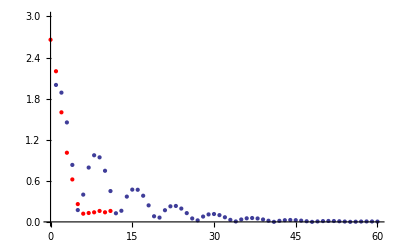

```mathematica
T1=20;
T2=20;
x0=2.0;
z0=0.65;
t=1;
p=180-Pi/90*14;
w=Cos[p];
w=0.7*(15)/90*Pi;
n=60;
x[0]=x0;
z[0]=z0;
xlist=Table[x0,{i,n}];
zlist=Table[z0,{i,n}];
For[i=2,i<=n,i++,xlist[[i]]=(E^(-t/T2)*(xlist[[(i-1)]]*Cos[p]*Exp[-t/T2]+zlist[[(i-1)]]*Sin[p]*Exp[-t/T1])//N);zlist[[i]]=((Exp[-t/T1]*(-xlist[[(i-1)]]*Sin[p]*Exp[-t/T2]+zlist[[(i-1)]]*Cos[p]*Exp[-t/T1]))//N)]
(For[i=2,i<=n,i++,xlist[[i]]=Abs[xlist[[i]]]])
fkt=Abs[q[tt]]/.DSolve[{q'[tt]==-1/(T1) q[tt]+w*y[tt],y'[tt]==-1/(T2) y[tt]-w*q[tt],q[0]==x0,y[0]==z0},{q[tt],y[tt]},tt];
Show[ListPlot[xlist,PlotRange->{{0,60},{0,3}}],ListPlot[cp02,PlotStyle->Red]]
```

```mathematica
fkt=Abs[q[tt]]/.DSolve[{q'[tt]==-1/(T1f) q[tt]+w*y[tt],y'[tt]==-1/(T2f) y[tt]-wf*q[tt],q[0]==x0f,y[0]==z0f},{q[tt],y[tt]},tt];
```

```mathematica
xlistforfit=Table[{i,xlist[[i]]},{i,Length[xlist]}];
```

```mathematica
Plot[fkt[[1]],{tt,0,60},PlotRange->{{0,60},{0,3}}]
```

-Graphics-

4.84214 | 4.84214
-153.367 | -153.367
0.47985 | 0.47985
1.68273 | 1.68273
1.42187 | 1.42187

{T1f→4.84214,T2f→-153.367,wf→0.47985,x0f→1.68273,z0f→1.42187}

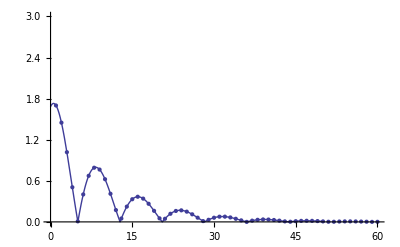

```mathematica
fit=NonlinearModelFit[xlistforfit,fkt[[1]],{T1f,T2f,wf,x0f,z0f},tt];
fit["ParameterConfidenceIntervals"]//TableForm
fit["BestFitParameters"]
Show[ListPlot[xlist,PlotRange->{{0,60},{0,3}}],Plot[Normal[fit],{tt,0,50},PlotRange->{{0,60},{0,3}}]]
```

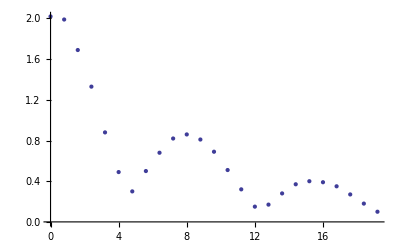

```mathematica
ListPlot[cp005]
```